# One Dimension

## Deterministic

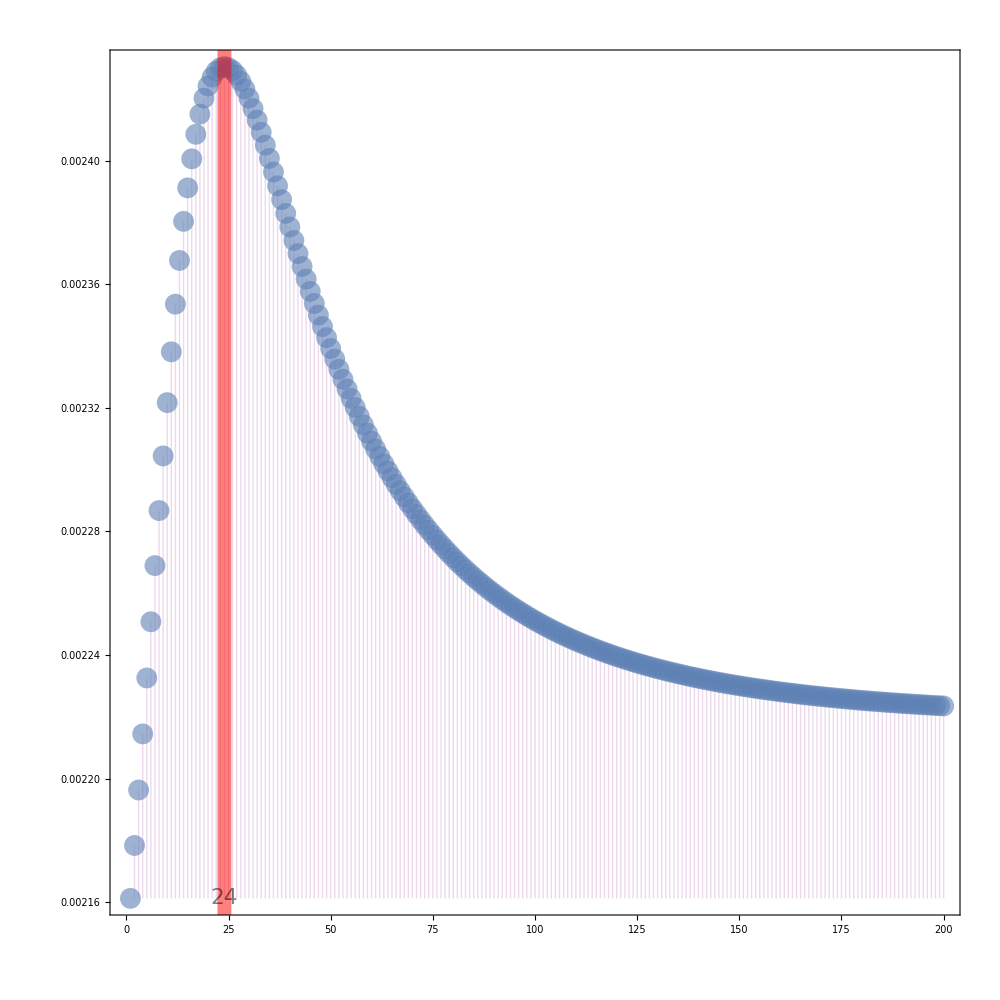

fitnessVSReleaseInterval.jpg

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["fitnessVSReleaseInterval01.csv"][[2;;All]];
{minFitness,maxFitness}={Min[data[[All,2]]],Max[data[[All,2]]]};
maxPosition=Cases[data,{a_,b_}/;b==maxFitness][[1,1]];
deterministic=ListPlot[{#[[1]],#[[2]]}&/@data
,AspectRatio->1
,Filling->Bottom
,FillingStyle->Directive[Purple,Opacity[.15],Thick]
,Frame->True
,1FrameLabel->({Style[Rotate[#,180Degree],35]&/@{"","Fitness"},Style[#,35]&/@{"","Release Interval: "<>ToString[maxPosition]}})
,FrameStyle->Directive[Gray,Thick]
,FrameTicksStyle->Directive[Gray,25]
,ImageSize->1000
,Joined->False
,PlotRange->Automatic
,PlotStyle->Directive[Opacity[.6],PointSize[.015]]
,Epilog->{
Red,Thickness[.01],Opacity[.5],Line[{{maxPosition,-minFitness*2},{maxPosition,maxFitness*2}}],
Black,Text[Style[ToString[maxPosition],21.5,Background->Directive[White,Opacity[1]]],{maxPosition,minFitness}]
}
]
Export["fitnessVSReleaseInterval.jpg",%,ImageSize->2500]
```

## Stochastic

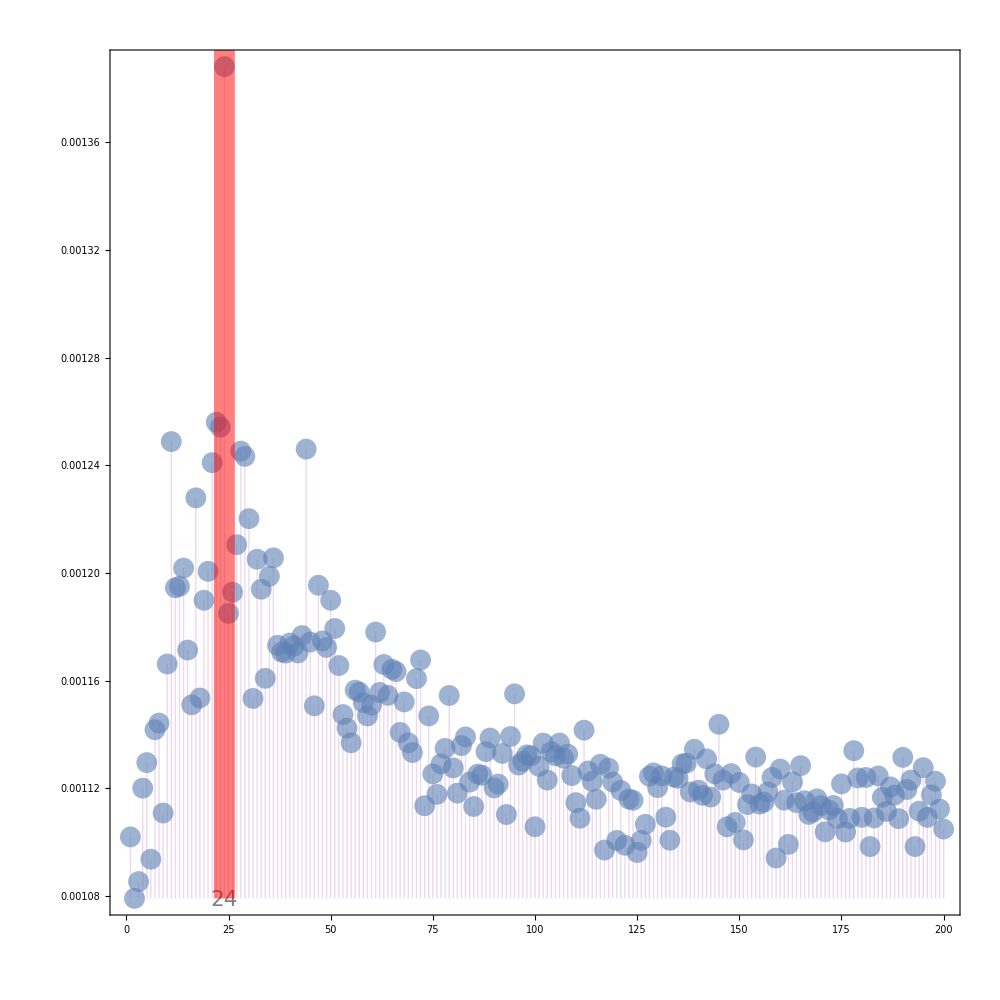

fitnessVSReleaseInterval.jpg

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["fitnessVSReleaseInterval02.csv"][[2;;All]];
{minFitness,maxFitness}={Min[data[[All,2]]],Max[data[[All,2]]]};
maxPosition=Cases[data,{a_,b_}/;b==maxFitness][[1,1]];
stochastic=ListPlot[data
,AspectRatio->1
,Filling->Bottom
,FillingStyle->Directive[Purple,Opacity[.15],Thick]
,Frame->True
,FrameLabel->({Style[Rotate[#,180Degree],35]&/@{"","Fitness"},Style[#,35]&/@{"","Release Interval"}})
,FrameStyle->Directive[Gray,Thick]
,FrameTicksStyle->Directive[Gray,25]
,ImageSize->1000
,Joined->False
,PlotRange->All
,PlotStyle->Directive[Opacity[.6],PointSize[.015]]
,Epilog->{
Red,Thickness[.015],Opacity[.5],Line[{{maxPosition,minFitness},{maxPosition,maxFitness*2}}],
Black,Text[Style[ToString[maxPosition],21.5,Background->Directive[White,Opacity[1]]],{maxPosition,minFitness*.99945}]
}
]
Export["fitnessVSReleaseInterval.jpg",%,ImageSize->2500]
```

## Both

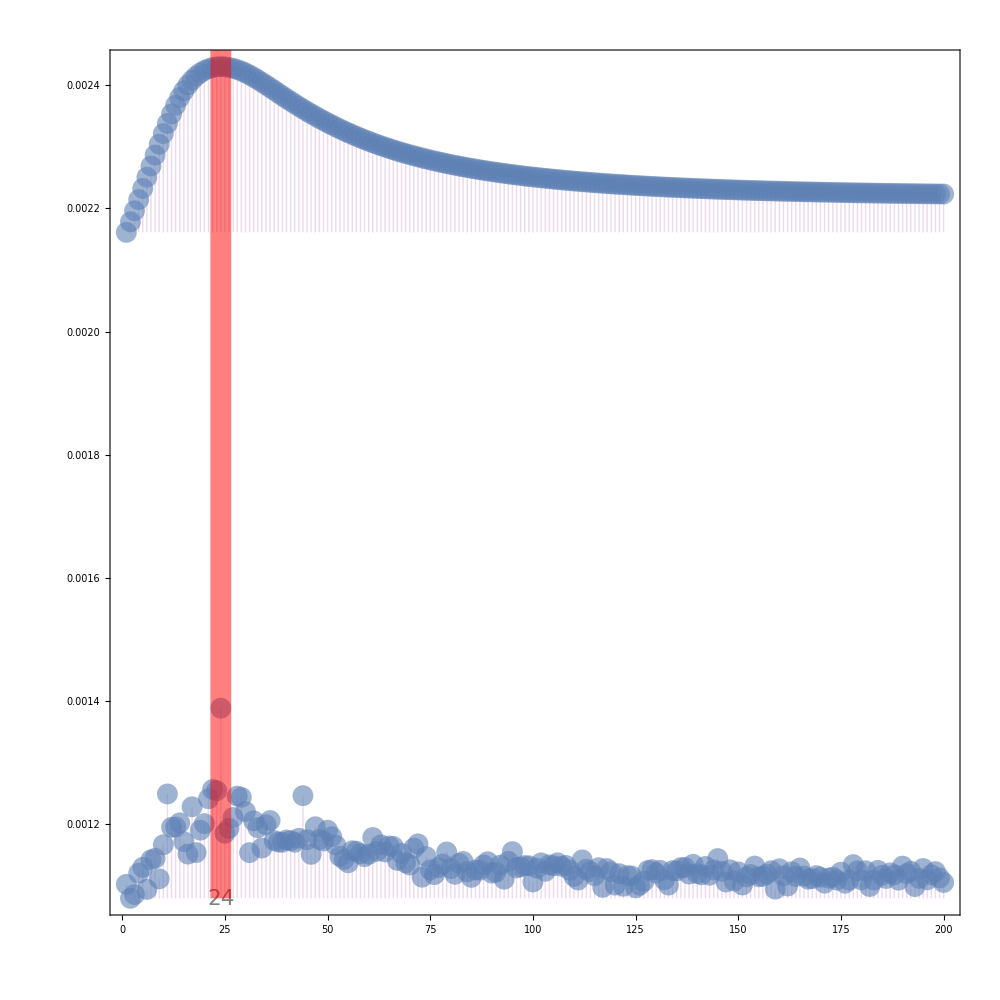

```mathematica
Show[{stochastic,deterministic},PlotRange->All]
```

# Two Dimensions

```mathematica
SetDirectory[NotebookDirectory[]]
rawTable=Import["fitnessVSReleaseIntervalVSReleaseNumber.csv"][[2;;All]][[All,2;;All]];
```

/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/ConstrainedOptimization/SingleNode/Translocations

```mathematica
CoolColor[ z_ ] :=RGBColor[z,0,2(1-z)];
ListPointPlot3D[Abs/@rawTable
,Axes->True
,AxesLabel->(Style[#,20,Gray]&/@{"RNumber","RInterval","Fitness"})
,Boxed->True
,BoxStyle->Directive[Thick,Opacity[.5]]
,ColorFunction->Function[{x,y,z},CoolColor[z]]
,Filling->Bottom
,FillingStyle->Directive[Opacity[.1]]
,ImageSize->1000
,PlotRange->All
,PlotStyle->Directive[Purple,Opacity[.35],PointSize[.003]]
,ViewPoint->{1,-1,1}
];
Export["responseSurface.pdf",%]
```

responseSurface.pdf

```mathematica
ListDensityPlot[Abs/@rawTable
,ColorFunction->ColorData[{"LakeColors","Reverse"}](*(Lighter[RGBColor[#,0,2(1-#)],.35]&)*)
,ColorFunctionScaling->True
,FrameLabel->(Style[#,40]&/@{"RNumber","RInterval"})
,FrameTicksStyle->Directive[20]
,ImageSize->1000
,InterpolationOrder->0
,PlotLegends->Automatic
]
Export["responseDensity.pdf",%]
```

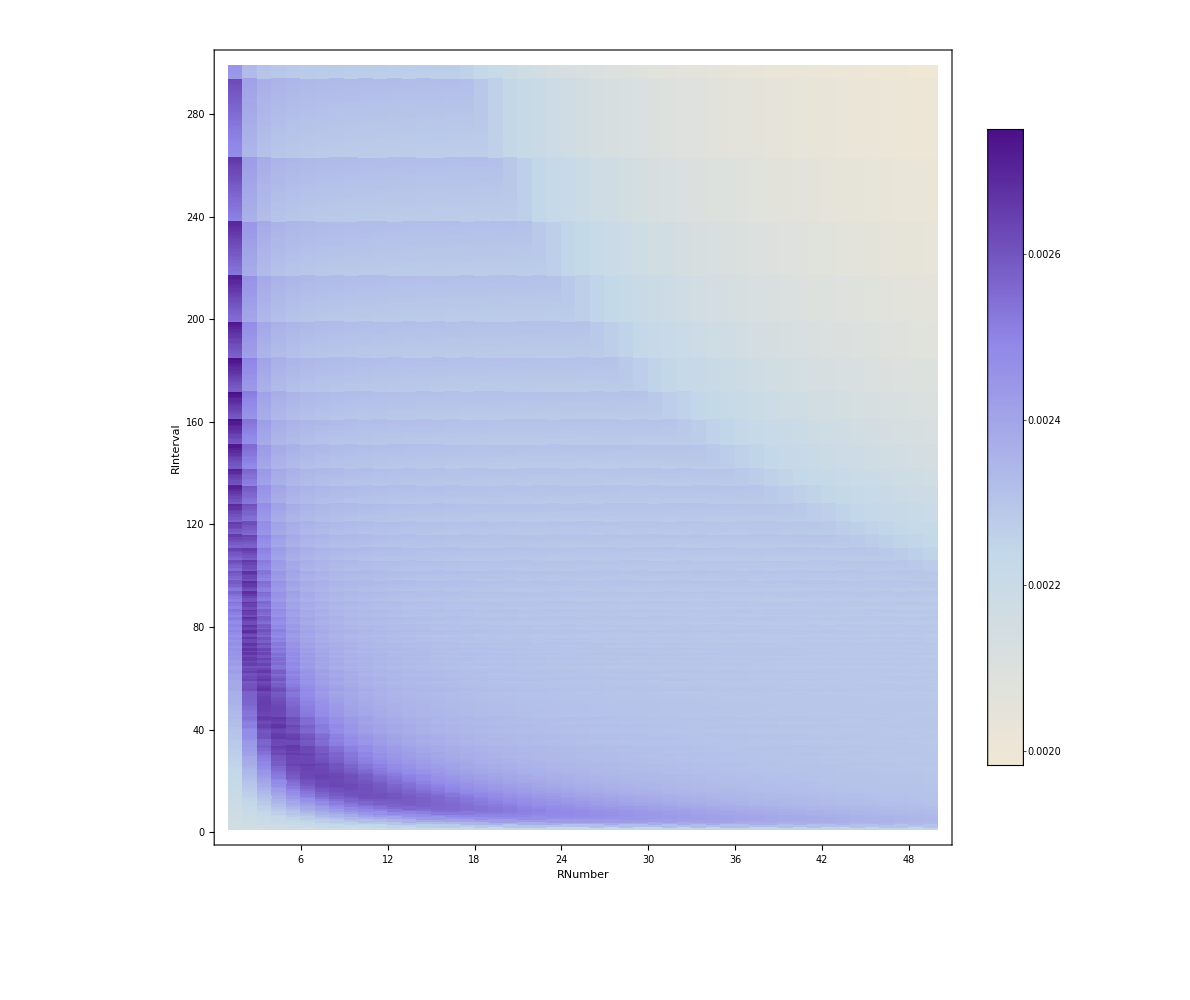

# Three Dimensions

## Analyses

```mathematica
SetDirectory[NotebookDirectory[]]
drive="UDMel";
rawTable=Import["ThreeWaySweep_"<>drive<>"_FixationFineNew.csv"];
{data,header}={rawTable[[2;;All,2;;All]],rawTable[[1]][[2;;All]]};
header
```

/Users/sanchez.hmsc/MGDrivE_Experiments/ConstrainedOptimization/SingleNode/TranslocationsAndUDMel

{MaleFemaleRatio,TimingInterval,ReleasesNumber,Fitness}

3D Plot

```mathematica
density=ListDensityPlot3D[data[[All,1;;4]]
,AxesLabel->(Style[#,20]&/@{"Male/Female","Timing","Releases"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData["LakeColors"]
,ImageSize->1000
,ImagePadding->All
,OpacityFunction->Interval[{0.5,.9}]
,PlotLabel->Style["HyperVolume: "<>ToString[Total[data[[All,4]]]],30]
,PlotLegends->None
,PlotRange->{All,{1,30},{6,All}}
,TicksStyle->Directive[Gray,15]
,ViewPoint->{Left,Bottom}(*{.25,1,-2.5}*)
];
Export[drive<>"/"<>drive<>"_fixationSurface3D"<>StringPadLeft[ToString[releases],3,"0"]<>".pdf",%]
```

UDMel/UDMel_fixationSurface3Dses.pdf

Releases Number

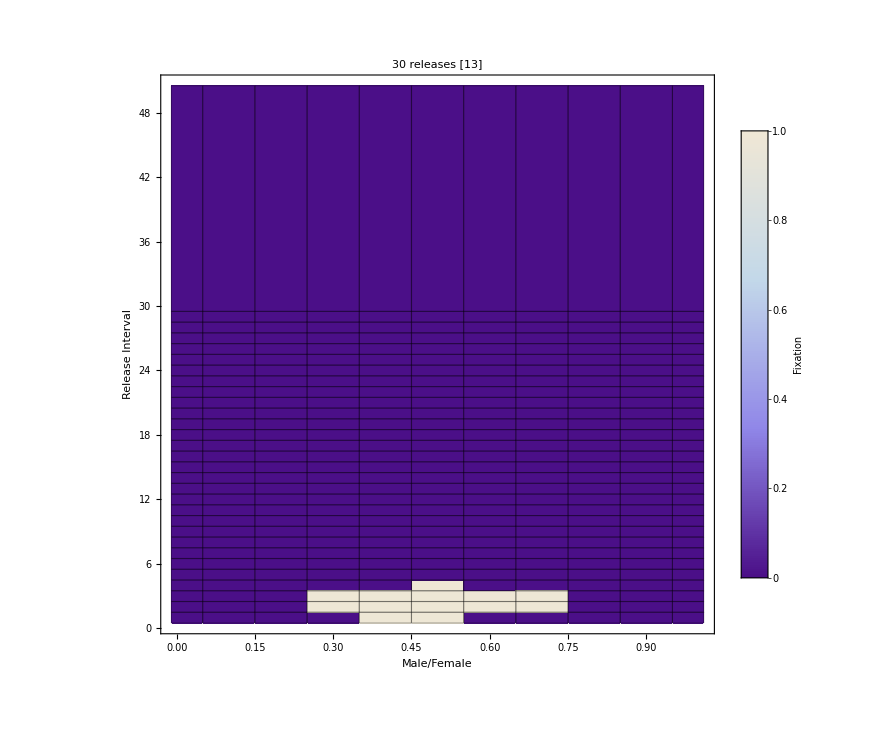

```mathematica
releases=30;
ClearAll[a,b,c]
subSample=Cases[data[[All,1;;4]],{a_,b_,releases,c_}->{a,b,c},1];
density=ListDensityPlot[subSample
,ClippingStyle->ColorData["LakeColors"][1]
,ColorFunction->ColorData[{"LakeColors",{0,1}}]
,ColorFunctionScaling->False
(*,ContourStyle->Directive[Thickness[.02],Opacity[.05]]*)
,FrameLabel->(Style[#,30]&/@{"Male/Female","Release Interval"})
,FrameStyle->Directive[Thick]
,FrameTicksStyle->20
,GridLines->{Range[-1,1,.1],Range[-1,101,5]}
,GridLinesStyle->Directive[Gray,White,Opacity[0]]
,ImageSize->750
,InterpolationOrder->0
,Mesh->All
,PlotLabel->Style[""<>ToString[releases]<>" releases "<>"["<>ToString[DeleteCases[Chop[subSample[[All,3]],.005],0]//Length]<>"]",30]
,PlotLegends->BarLegend[{"LakeColors",{0,1}},LegendLabel->Style["Fixation",Gray,25],LegendMargins->5,LabelStyle->{FontSize->20}]
,PlotRange->{{-.01,1.01},{.5,50.5}}
,Epilog->Flatten[{Opacity[0],PointSize[.0075],Point[#]&/@subSample[[All,1;;2]]}]
]
(*Export[drive<>"/"<>drive<>"fixationSurface"<>StringPadLeft[ToString[releases],3,"0"]<>".png",%]*)
```

Male to Female Ratio

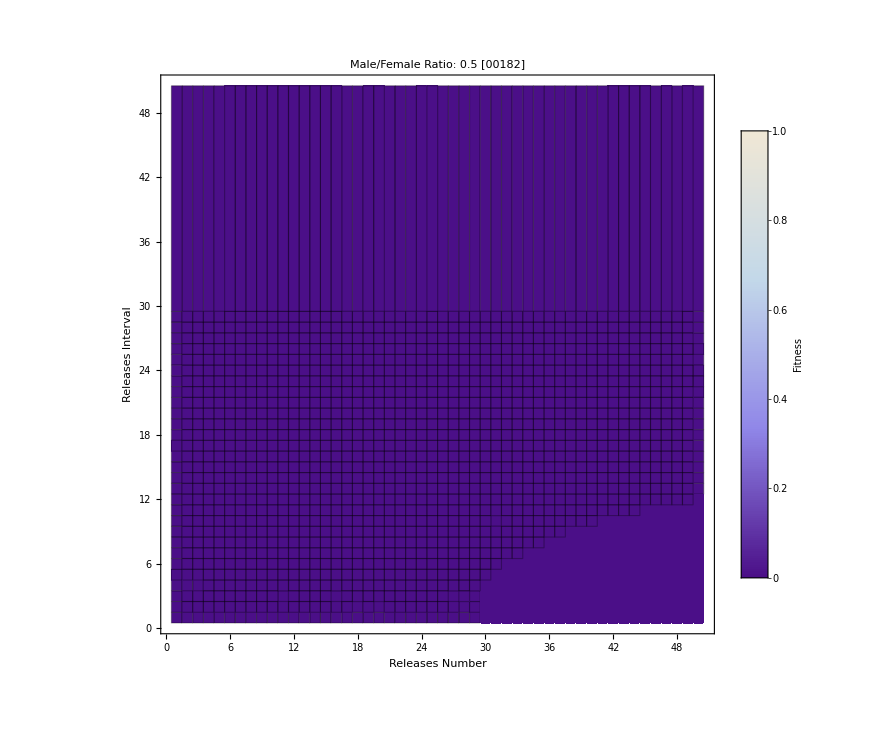
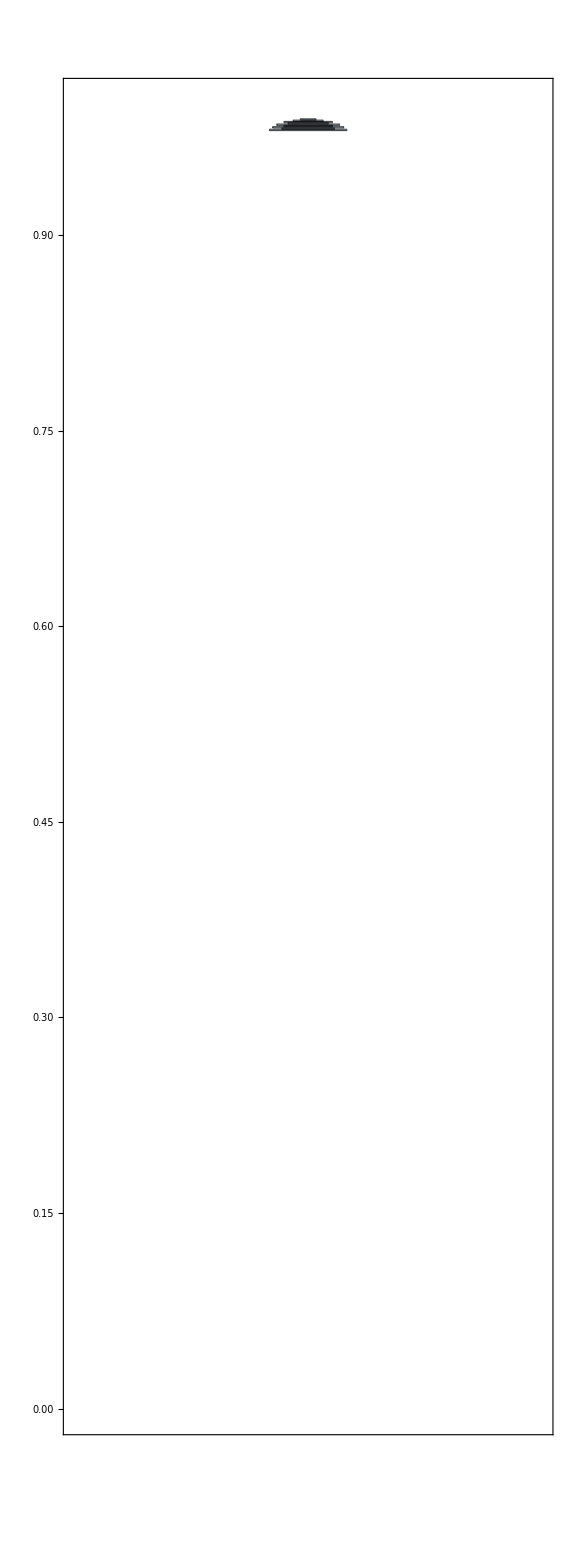
-Graphics- | 		 | -Graphics-

```mathematica
maleFemaleRatio=.5;
ClearAll[a,b,c]
subSample=Cases[data[[All,1;;4]],{maleFemaleRatio,b_,a_,c_}->{a,b,c},1];
density=ListDensityPlot[subSample
,ClippingStyle->ColorData["LakeColors"][0]
,ColorFunction->ColorData[{"LakeColors",{0,1}}]
,ColorFunctionScaling->False
(*,ContourStyle->Directive[Thickness[.02],Opacity[.05]]*)
,FrameLabel->(Style[#,30]&/@{"Releases Number","Releases Interval"})
,FrameStyle->Directive[Thick]
,FrameTicksStyle->20
,GridLines->{Range[0,100,10],Range[0,100,10]}
,GridLinesStyle->Directive[Gray,White,Opacity[0]]
,ImageSize->750
,InterpolationOrder->0
,Mesh->All
,PlotLegends->BarLegend[{"LakeColors",{0,1}},LegendLabel->Style["Fitness",Gray,25],LegendMargins->5,LabelStyle->{FontSize->20}]
,PlotLabel->Style[""<>" Male/Female Ratio: "<>ToString[maleFemaleRatio]<>""<>" ["<>StringPadLeft[ToString[DeleteCases[Chop[subSample[[All,3]],.005],0]//Total//Round],5,"0"]<>"]",30]
,PlotRange->{{.5,50.5},{.5,50.5}}
,Epilog->Flatten[{Opacity[0],PointSize[.0075],Point[#]&/@subSample[[All,1;;2]]}]
];
distributionChart=DistributionChart[
DeleteCases[Chop[subSample[[All,3]],.005],0]
,AspectRatio->3
,ChartStyle->Directive[LightBlue,EdgeForm[{Black,Thick}]]
,ChartElementFunction->"HistogramDensity"
,FrameStyle->Thick
,FrameTicksStyle->20
,ImageSize->Large
,PlotRange->{0,1}
];
Grid[{{density,"\t\t",distributionChart}}]
```

Fitness Explorer

```mathematica
maxSamples=25;
{femalesMax,releasesMax}={0,50};
subSample=Cases[data[[All,1;;5]],{females_,_,releases_,fitness_,fixation_}/;(females≤femalesMax &&releasesMax≥releases &&fixation==1)];
Prepend[Sort[subSample,#1[[4]]>#2[[4]]&],header][[1;;maxSamples]]//Grid[#,Background->{None,{LightBlue,None}},Frame->True]&
```

Part::take: Cannot take positions 1 through 5 in {0,0,0,0}.

Part::take: Cannot take positions 1 through 25 in {{MaleFemaleRatio,TimingInterval,ReleasesNumber,Fitness}}.

Grid[{{MaleFemaleRatio,TimingInterval,ReleasesNumber,Fitness}}⟦1;;25⟧,Background→{None,{RGBColor[0.87, 0.94, 1],None}},Frame→True]

## Export Plots

```mathematica
frames=Table[
releases=i;
Clear[a,b,c];
subSample=Cases[data[[All,1;;4]],{a_,b_,releases,c_}->{a,b,c},1];
densityPlot=ListDensityPlot[subSample
,ClippingStyle->ColorData["LakeColors"][1]
,ColorFunction->ColorData[{"LakeColors",{0,1}}]
,ColorFunctionScaling->False
(*,ContourStyle->Directive[Thickness[.02],Opacity[.05]]*)
,FrameLabel->(Style[#,30]&/@{"Male/Female Ratio","Releases Interval"})
,FrameStyle->Directive[Thick]
,FrameTicksStyle->Directive[Gray,20]
,GridLines->{Range[-1,2,.1],Range[0,100,5]}
,GridLinesStyle->Directive[Gray,White,Opacity[0]]
,ImageSize->1000
,InterpolationOrder->0
,Mesh->All
,MeshStyle->Directive[White,Thickness[.00075],Opacity[.75]]
,PlotLabel->Style[""<>ToString[releases]<>" releases "<>"["<>StringPadLeft[ToString[DeleteCases[Chop[subSample[[All,3]],.005],0]//Length],5,"0"]<>"]",30]
(*,PlotLegends->BarLegend[{"LakeColors",{0,1}},LegendLabel->Style["Fitness",Black,20],LegendMargins->5,LabelStyle->{FontSize->10}]*)
,PlotRange->{{-.01,1.01},{.5,50.5}}
,Epilog->Flatten[{Opacity[0],PointSize[.0075],Point[#]&/@subSample[[All,1;;2]]}]
];
Export[drive<>"/"<>drive<>"_ReleasesNumber"<>StringPadLeft[ToString[releases],3,"0"]<>".pdf",densityPlot];
,{i,1,50}];
```

```mathematica
maleFemaleRatios=DeleteDuplicates[data[[All,1]]];
frames=Table[
maleFemaleRatio=maleFemaleRatios[[i]];
subSample=Cases[data[[All,1;;4]],{maleFemaleRatio,b_,a_,c_}->{a,b,c},1];
densityPlot=ListDensityPlot[subSample
,ClippingStyle->ColorData["LakeColors"][0]
,ColorFunction->ColorData[{"LakeColors",{0,1}}]
,ColorFunctionScaling->True
(*,ContourStyle->Directive[Thickness[.02],Opacity[.05]]*)
,FrameLabel->(Style[#,30]&/@{"Releases Number","Releases Interval"})
,FrameStyle->Directive[Thick]
,FrameTicksStyle->Directive[Gray,20]
,GridLines->{Range[0,1,.1],Range[0,100,5]}
,GridLinesStyle->Directive[Gray,White,Opacity[0]]
,ImageSize->1000
,InterpolationOrder->0
,Mesh->All
,MeshStyle->Directive[White,Thickness[.00075],Opacity[.75]]
,PlotLegends->None(*BarLegend[{"LakeColors",{0,1}},LegendLabel->Style["Fitness",Black,20],LegendMargins->5,LabelStyle->{FontSize->10}]*)
,PlotLabel->Style[""<>" Male/Female Ratio: "<>ToString[maleFemaleRatio]<>""<>" ["<>StringPadLeft[ToString[DeleteCases[Chop[subSample[[All,3]],.005],0]//Total//Round],5,"0"]<>"]",30]
,PlotRange->{{.5,50.5},{.5,50.5}}
,Epilog->Flatten[{Opacity[0],PointSize[.0075],Point[#]&/@subSample[[All,1;;2]]}]
];
Export[drive<>"/"<>drive<>"_MaleToFemale"<>StringPadLeft[ToString[Round[maleFemaleRatio*100]],3,"0"]<>".pdf",densityPlot];
densityPlot
,{i,1,maleFemaleRatios//Length}];
(*Export[drive<>"/"<>drive<>"fixationSurface02"<>".gif",frames,"DisplayDurations"->2]*)
```

```mathematica
grid=Grid[Partition[frames,11]];
Export[drive<>"/"<>drive<>"_MaleToFemale_Grid.pdf",grid]
```

Translocations/Translocations_MaleToFemale_Grid.pdf

## Other Routines

```mathematica
densitySlice=ListSliceDensityPlot3D[data,"BackPlanes"
,AxesLabel->(Style[#,20]&/@{"Male/Female","Timing","Releases"})
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,ImageSize->1000
,ImagePadding->All
,PlotLegends->None
,PlotRange->{All,{1,All},{5,All}}
,TicksStyle->Directive[Gray,15]
,ViewPoint->{1,1,-1}
];
contour=ListContourPlot3D[data
,AxesLabel->(Style[#,20]&/@header[[1;;3]])
,BoxRatios->{1,1,1}
,BoxStyle->Directive[{Gray,Thick}]
,ColorFunction->ColorData["LakeColors"]
,Contours->3
,ContourStyle->Directive[Opacity[.25]]
,ImageSize->1000
,ImagePadding->All
,Mesh->None
,PlotLegends->None
,TicksStyle->Directive[Gray,15]
,ViewPoint->{1,1,-1}
];
Show[density,densitySlice];
```

```mathematica
timing=15;
subSample=Cases[data,{a_,timing,b_,c_}->{a,b,c}];
ListDensityPlot[subSample
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,ImageSize->750
,FrameLabel->{"Male/Female","Release Number"}
];
```